```mathematica
RSolve[{(n+1)f[n+1]==(n-1/2)f[n]-(n-2)f[n-1],f[2]==3/2,f[3]==3/4},f[n],n]
```

{{f[n]→4 GegenbauerC[n,-1/2,1/2]}}

```mathematica
4 GegenbauerC[n,-1/2,1/2]/.{{f[n]->4 GegenbauerC[n,-1/2,1/2]}}
```

{4 GegenbauerC[n,-1/2,1/2]}

```mathematica
First[{4 GegenbauerC[n,-1/2,1/2]}]
```

4 GegenbauerC[n,-1/2,1/2]

```mathematica
FullSimplify[4 GegenbauerC[n,-1/2,1/2]]
```

4 GegenbauerC[n,-1/2,1/2]

```mathematica
∑_(n=1)^∞ 4 GegenbauerC[n,-1/2,1/2]
```

$Aborted

```mathematica
f[n_]:=4 GegenbauerC[n,-1/2,1/2]
```

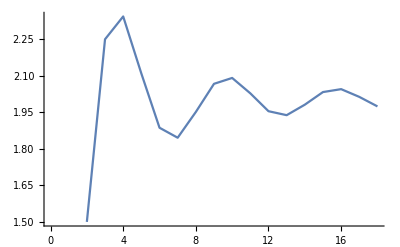

```mathematica
ListLinePlot[Table[{n,Sum[f[x],{x,2,n}]},{n,2,18}]]
```

```mathematica
qq[x_]:=InterpolatingPolynomial[Table[{n,Sum[f[x],{x,2,n}]},{n,2,18}]]
```

SetDelayed::write: Tag Plus in (3/2+(3/4+(-21/64+(7/128+Times[«2»]) (-4+x)) (-3+x)) (-2+x))[x_] is Protected.

$Failed

```mathematica
InterpolatingFunction[{{2,3/2},{3,9/4},{4,75/32},{5,135/64},{6,483/256},{7,945/512},{8,15987/8192},{9,33867/16384},{10,137049/65536},{11,265815/131072},{12,2049567/1048576},{13,4064931/2097152},{14,16621275/8388608},{15,34112241/16777216},{16,1098012099/536870912},{17,2161894131/1073741824},{18,8479630365/4294967296}}]
```

InterpolatingFunction[{{2,3/2},{3,9/4},{4,75/32},{5,135/64},{6,483/256},{7,945/512},{8,15987/8192},{9,33867/16384},{10,137049/65536},{11,265815/131072},{12,2049567/1048576},{13,4064931/2097152},{14,16621275/8388608},{15,34112241/16777216},{16,1098012099/536870912},{17,2161894131/1073741824},{18,8479630365/4294967296}}]

```mathematica
ifun = InterpolatingFunction[Table[{n,Sum[f[x],{x,2,n}]},{n,2,18}]]
```

InterpolatingFunction[{{2,3/2},{3,9/4},{4,75/32},{5,135/64},{6,483/256},{7,945/512},{8,15987/8192},{9,33867/16384},{10,137049/65536},{11,265815/131072},{12,2049567/1048576},{13,4064931/2097152},{14,16621275/8388608},{15,34112241/16777216},{16,1098012099/536870912},{17,2161894131/1073741824},{18,8479630365/4294967296}}]

```mathematica
ifun[2]
```

InterpolatingFunction[{{2,3/2},{3,9/4},{4,75/32},{5,135/64},{6,483/256},{7,945/512},{8,15987/8192},{9,33867/16384},{10,137049/65536},{11,265815/131072},{12,2049567/1048576},{13,4064931/2097152},{14,16621275/8388608},{15,34112241/16777216},{16,1098012099/536870912},{17,2161894131/1073741824},{18,8479630365/4294967296}}][2]

```mathematica
points=Table[{n,Sum[f[x],{x,2,n}]},{n,2,18}]
```

{{2,3/2},{3,9/4},{4,75/32},{5,135/64},{6,483/256},{7,945/512},{8,15987/8192},{9,33867/16384},{10,137049/65536},{11,265815/131072},{12,2049567/1048576},{13,4064931/2097152},{14,16621275/8388608},{15,34112241/16777216},{16,1098012099/536870912},{17,2161894131/1073741824},{18,8479630365/4294967296}}

```mathematica
FindFit[points]
```

FindFit::argr: FindFit called with 1 argument; 4 arguments are expected.

FindFit[{{2,3/2},{3,9/4},{4,75/32},{5,135/64},{6,483/256},{7,945/512},{8,15987/8192},{9,33867/16384},{10,137049/65536},{11,265815/131072},{12,2049567/1048576},{13,4064931/2097152},{14,16621275/8388608},{15,34112241/16777216},{16,1098012099/536870912},{17,2161894131/1073741824},{18,8479630365/4294967296}}]

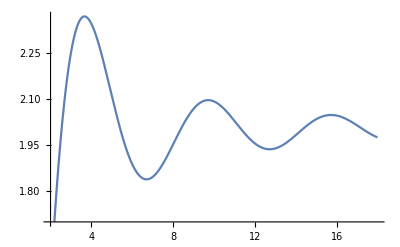

```mathematica
Plot[-(11502661227/4294967296)+(3878205273906479*(x))/1031822943191040-(145277086875750023*(x)^2)/78793752025497600+(29360380373061298109*(x)^3)/26001938168414208000-(6974106587907224299*(x)^4)/12735643184529408000+(26102226504433067*(x)^5)/146949729052262400-(340487654624651311*(x)^6)/8229184826926694400+(27435542161877377*(x)^7)/3740538557693952000-(209554833445935407*(x)^8)/209470159230861312000+(271002566456911*(x)^9)/2618376990385766400-(11922665261359*(x)^10)/1496215423077580800+(658076306671*(x)^11)/1469497290522624000-(268322504627*(x)^12)/14962154230775808000+(3766146859*(x)^13)/7641385910717644800-(2606449121*(x)^14)/299542327700131676160+(324286219*(x)^15)/3744279096251645952000-(1496471*(x)^16)/4279176110001881088000,{x,2,18}]
```

```mathematica
Series[ifu[x],{x,2,8}]
```

3/2+(19 (x-2))/16-63/128 (x-2)^2+7/128 (x-2)^3+O[x-2]^9

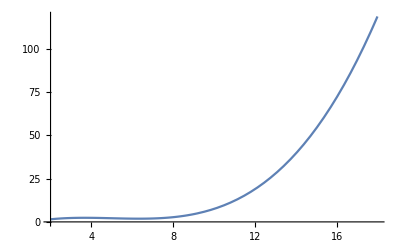

```mathematica
Plot[3/2+(19 (x-2))/16-63/128 (x-2)^2+7/128 (x-2)^3,{x,2,18}]
```

```mathematica
InterpolatingPolynomial[Table[{n,Sum[f[x],{x,2,n}]},{n,2,20}],x]
```

3/2+(3/4+(-21/64+(7/128+(1/2048+(-31/20480+(401/1966080+(-53/27525120+(-1997/880803840+(109/452984832+(-509/181193932800+(-39901/27903865651200+(166121/1339385551257600+(-48863/34824024332697600+(-285463/624046516041940992+(15656947/468034887031455744000+(-1496471/4279176110001881088000+(-12211747/145491987740063956992000+(777245047 (-19+x))/146655923641984468647936000) (-18+x)) (-17+x)) (-16+x)) (-15+x)) (-14+x)) (-13+x)) (-12+x)) (-11+x)) (-10+x)) (-9+x)) (-8+x)) (-7+x)) (-6+x)) (-5+x)) (-4+x)) (-3+x)) (-2+x)

```mathematica
qqq[x_]:=3/2+(3/4+(-21/64+(7/128+(1/2048+(-31/20480+(401/1966080+(-53/27525120+(-1997/880803840+(109/452984832+(-509/181193932800+(-39901/27903865651200+(166121/1339385551257600+(-48863/34824024332697600+(-285463/624046516041940992+(15656947/468034887031455744000+(-1496471/4279176110001881088000+(-12211747/145491987740063956992000+(777245047 (-19+x))/146655923641984468647936000) (-18+x)) (-17+x)) (-16+x)) (-15+x)) (-14+x)) (-13+x)) (-12+x)) (-11+x)) (-10+x)) (-9+x)) (-8+x)) (-7+x)) (-6+x)) (-5+x)) (-4+x)) (-3+x)) (-2+x)
```

```mathematica
qq[2]
```

(3/2+(3/4+(-21/64+(7/128+(1/2048+(-31/20480+(401/1966080+(-53/27525120+(-1997/880803840+(109/452984832+(-509/181193932800+(-39901/27903865651200+(166121/1339385551257600+(-48863/34824024332697600+(-285463/624046516041940992+(15656947/468034887031455744000-(1496471 (-17+x))/4279176110001881088000) (-16+x)) (-15+x)) (-14+x)) (-13+x)) (-12+x)) (-11+x)) (-10+x)) (-9+x)) (-8+x)) (-7+x)) (-6+x)) (-5+x)) (-4+x)) (-3+x)) (-2+x))[2]

```mathematica
qqq[2]
```

3/2

```mathematica
Numerator[3/2]
```

3

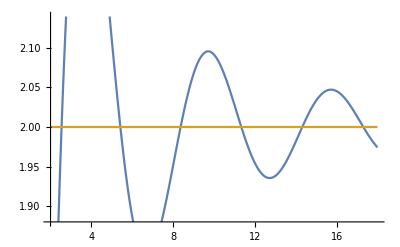

```mathematica
Plot[{qqq[x],2.0},{x,2,18},PlotPoints->1000]
```

```mathematica
3/2+(3/4+(-21/64+(7/128+(1/2048+(-31/20480+(401/1966080+(-53/27525120+(-1997/880803840+(109/452984832+(-509/181193932800+(-39901/27903865651200+(166121/1339385551257600+(-48863/34824024332697600+(-285463/624046516041940992+(15656947/468034887031455744000-(1496471 (-17+x))/4279176110001881088000) (-16+x)) (-15+x)) (-14+x)) (-13+x)) (-12+x)) (-11+x)) (-10+x)) (-9+x)) (-8+x)) (-7+x)) (-6+x)) (-5+x)) (-4+x)) (-3+x)) (-2+x)//Simplify
```

3/2+(-2+x) (3/4+(-3+x) (-21/64-1/29954232770013167616000(-4+x) (-885424676492708352000+748144628291312582400 x-749134262292335658720 x^2+280289209960473612552 x^3-67717760285964338084 x^4+12011622137165225642 x^5-1555159780553427085 x^6+143637825728065081 x^7-9320731320541737 x^8+417922242790161 x^9-12557191955095 x^10+237872445667 x^11-2500012079 x^12+10475297 x^13)))

```mathematica
Expand[%26]
```

-11502661227/4294967296+(3878205273906479 x)/1031822943191040-(145277086875750023 x^2)/78793752025497600+(29360380373061298109 x^3)/26001938168414208000-(6974106587907224299 x^4)/12735643184529408000+(26102226504433067 x^5)/146949729052262400-(340487654624651311 x^6)/8229184826926694400+(27435542161877377 x^7)/3740538557693952000-(209554833445935407 x^8)/209470159230861312000+(271002566456911 x^9)/2618376990385766400-(11922665261359 x^10)/1496215423077580800+(658076306671 x^11)/1469497290522624000-(268322504627 x^12)/14962154230775808000+(3766146859 x^13)/7641385910717644800-(2606449121 x^14)/299542327700131676160+(324286219 x^15)/3744279096251645952000-(1496471 x^16)/4279176110001881088000

```mathematica
<<FourierSeries`
```

```mathematica
NFourierTrigSeries[Out[27],x,9,FourierParameters->{2,18}]
```

1/3 √π (-9.1297+0.0776019 Cos[18 x]-0.0195598 Cos[36 x]+0.00870646 Cos[54 x]-0.00489999 Cos[72 x]+0.00313676 Cos[90 x]-0.0021786 Cos[108 x]+0.00160073 Cos[126 x]-0.00122562 Cos[144 x]+0.000968429 Cos[162 x]+1.41879 Sin[18 x]-0.712357 Sin[36 x]+0.475273 Sin[54 x]-0.356552 Sin[72 x]+0.285277 Sin[90 x]-0.237747 Sin[108 x]+0.203792 Sin[126 x]-0.178323 Sin[144 x]+0.158512 Sin[162 x])

```mathematica
Simplify[1/3 √π (((362880-60480 π^2+3024 π^4-72 π^6+π^8) Sin[18 x])/(16529940864 √π)+((-2835+1890 π^2-378 π^4+36 π^6-2 π^8) Sin[36 x])/(66119763456 √π))]
```

(4 (362880-60480 π^2+3024 π^4-72 π^6+π^8) Sin[18 x]+(-2835+1890 π^2-378 π^4+36 π^6-2 π^8) Sin[36 x])/198359290368

```mathematica
Table[{x,qqq[x]},{x,2,18,0.01}]
```

{{2.,1.5},{2.01,1.51132},{2.02,1.52257},{2.03,1.53374},{2.04,1.54483},{2.05,1.55585},{2.06,1.56678},{2.07,1.57764},{2.08,1.58842},{2.09,1.59913},{2.1,1.60975},{2.11,1.6203},{2.12,1.63077},{2.13,1.64116},{2.14,1.65147},{2.15,1.6617},{2.16,1.67186},{2.17,1.68193},{2.18,1.69193},{2.19,1.70185},{2.2,1.71169},{2.21,1.72146},{2.22,1.73114},{2.23,1.74075},{2.24,1.75027},{2.25,1.75972},{2.26,1.76909},{2.27,1.77838},{2.28,1.7876},{2.29,1.79673},{2.3,1.80579},{2.31,1.81476},{2.32,1.82366},{2.33,1.83248},{2.34,1.84123},{2.35,1.84989},{2.36,1.85848},{2.37,1.86698},{2.38,1.87541},{2.39,1.88376},{2.4,1.89204},{2.41,1.90023},{2.42,1.90835},{2.43,1.91639},{2.44,1.92435},{2.45,1.93223},{2.46,1.94004},{2.47,1.94776},{2.48,1.95541},{2.49,1.96299},{2.5,1.97048},{2.51,1.9779},{2.52,1.98524},{2.53,1.99251},{2.54,1.9997},{2.55,2.00681},{2.56,2.01384},{2.57,2.0208},{2.58,2.02768},{2.59,2.03449},{2.6,2.04122},{2.61,2.04787},{2.62,2.05445},{2.63,2.06095},{2.64,2.06738},{2.65,2.07373},{2.66,2.08001},{2.67,2.08621},{2.68,2.09234},{2.69,2.09839},{2.7,2.10436},{2.71,2.11027},{2.72,2.1161},{2.73,2.12185},{2.74,2.12753},{2.75,2.13314},{2.76,2.13867},{2.77,2.14413},{2.78,2.14952},{2.79,2.15484},{2.8,2.16008},{2.81,2.16525},{2.82,2.17035},{2.83,2.17537},{2.84,2.18032},{2.85,2.18521},{2.86,2.19002},{2.87,2.19476},{2.88,2.19942},{2.89,2.20402},{2.9,2.20855},{2.91,2.21301},{2.92,2.21739},{2.93,2.22171},{2.94,2.22596},{2.95,2.23014},{2.96,2.23425},{2.97,2.23829},{2.98,2.24226},{2.99,2.24616},{3.,2.25},{3.01,2.25377},{3.02,2.25747},{3.03,2.2611},{3.04,2.26467},{3.05,2.26817},{3.06,2.2716},{3.07,2.27497},{3.08,2.27827},{3.09,2.28151},{3.1,2.28468},{3.11,2.28778},{3.12,2.29082},{3.13,2.2938},{3.14,2.29671},{3.15,2.29956},{3.16,2.30235},{3.17,2.30507},{3.18,2.30773},{3.19,2.31032},{3.2,2.31286},{3.21,2.31533},{3.22,2.31774},{3.23,2.32009},{3.24,2.32237},{3.25,2.3246},{3.26,2.32677},{3.27,2.32887},{3.28,2.33092},{3.29,2.33291},{3.3,2.33483},{3.31,2.3367},{3.32,2.33851},{3.33,2.34026},{3.34,2.34196},{3.35,2.34359},{3.36,2.34517},{3.37,2.3467},{3.38,2.34816},{3.39,2.34957},{3.4,2.35093},{3.41,2.35222},{3.42,2.35347},{3.43,2.35466},{3.44,2.35579},{3.45,2.35687},{3.46,2.3579},{3.47,2.35887},{3.48,2.35979},{3.49,2.36066},{3.5,2.36147},{3.51,2.36224},{3.52,2.36295},{3.53,2.36361},{3.54,2.36422},{3.55,2.36478},{3.56,2.36528},{3.57,2.36574},{3.58,2.36615},{3.59,2.36651},{3.6,2.36683},{3.61,2.36709},{3.62,2.3673},{3.63,2.36747},{3.64,2.36759},{3.65,2.36767},{3.66,2.3677},{3.67,2.36768},{3.68,2.36761},{3.69,2.3675},{3.7,2.36735},{3.71,2.36715},{3.72,2.36691},{3.73,2.36662},{3.74,2.36629},{3.75,2.36592},{3.76,2.3655},{3.77,2.36504},{3.78,2.36454},{3.79,2.364},{3.8,2.36342},{3.81,2.3628},{3.82,2.36213},{3.83,2.36143},{3.84,2.36069},{3.85,2.35991},{3.86,2.35909},{3.87,2.35823},{3.88,2.35733},{3.89,2.3564},{3.9,2.35542},{3.91,2.35442},{3.92,2.35337},{3.93,2.35229},{3.94,2.35117},{3.95,2.35002},{3.96,2.34884},{3.97,2.34762},{3.98,2.34636},{3.99,2.34507},{4.,2.34375},{4.01,2.3424},{4.02,2.34101},{4.03,2.33959},{4.04,2.33814},{4.05,2.33666},{4.06,2.33514},{4.07,2.3336},{4.08,2.33203},{4.09,2.33042},{4.1,2.32879},{4.11,2.32713},{4.12,2.32544},{4.13,2.32372},{4.14,2.32198},{4.15,2.3202},{4.16,2.3184},{4.17,2.31658},{4.18,2.31472},{4.19,2.31284},{4.2,2.31094},{4.21,2.30901},{4.22,2.30706},{4.23,2.30508},{4.24,2.30308},{4.25,2.30105},{4.26,2.299},{4.27,2.29693},{4.28,2.29484},{4.29,2.29272},{4.3,2.29059},{4.31,2.28843},{4.32,2.28625},{4.33,2.28405},{4.34,2.28183},{4.35,2.27959},{4.36,2.27734},{4.37,2.27506},{4.38,2.27276},{4.39,2.27045},{4.4,2.26812},{4.41,2.26577},{4.42,2.26341},{4.43,2.26102},{4.44,2.25863},{4.45,2.25621},{4.46,2.25378},{4.47,2.25134},{4.48,2.24888},{4.49,2.2464},{4.5,2.24392},{4.51,2.24141},{4.52,2.2389},{4.53,2.23637},{4.54,2.23383},{4.55,2.23128},{4.56,2.22872},{4.57,2.22614},{4.58,2.22355},{4.59,2.22096},{4.6,2.21835},{4.61,2.21573},{4.62,2.2131},{4.63,2.21046},{4.64,2.20782},{4.65,2.20516},{4.66,2.2025},{4.67,2.19983},{4.68,2.19715},{4.69,2.19446},{4.7,2.19177},{4.71,2.18907},{4.72,2.18637},{4.73,2.18365},{4.74,2.18094},{4.75,2.17821},{4.76,2.17549},{4.77,2.17275},{4.78,2.17002},{4.79,2.16728},{4.8,2.16453},{4.81,2.16179},{4.82,2.15904},{4.83,2.15628},{4.84,2.15353},{4.85,2.15077},{4.86,2.14801},{4.87,2.14525},{4.88,2.14249},{4.89,2.13973},{4.9,2.13696},{4.91,2.1342},{4.92,2.13144},{4.93,2.12868},{4.94,2.12591},{4.95,2.12315},{4.96,2.12039},{4.97,2.11764},{4.98,2.11488},{4.99,2.11213},{5.,2.10938},{5.01,2.10663},{5.02,2.10388},{5.03,2.10114},{5.04,2.0984},{5.05,2.09567},{5.06,2.09294},{5.07,2.09021},{5.08,2.08749},{5.09,2.08477},{5.1,2.08206},{5.11,2.07936},{5.12,2.07666},{5.13,2.07396},{5.14,2.07128},{5.15,2.0686},{5.16,2.06592},{5.17,2.06326},{5.18,2.0606},{5.19,2.05794},{5.2,2.0553},{5.21,2.05266},{5.22,2.05004},{5.23,2.04742},{5.24,2.04481},{5.25,2.04221},{5.26,2.03961},{5.27,2.03703},{5.28,2.03446},{5.29,2.0319},{5.3,2.02934},{5.31,2.0268},{5.32,2.02427},{5.33,2.02175},{5.34,2.01924},{5.35,2.01674},{5.36,2.01425},{5.37,2.01178},{5.38,2.00931},{5.39,2.00686},{5.4,2.00442},{5.41,2.00199},{5.42,1.99958},{5.43,1.99718},{5.44,1.99479},{5.45,1.99242},{5.46,1.99005},{5.47,1.98771},{5.48,1.98537},{5.49,1.98305},{5.5,1.98075},{5.51,1.97845},{5.52,1.97618},{5.53,1.97391},{5.54,1.97167},{5.55,1.96943},{5.56,1.96722},{5.57,1.96501},{5.58,1.96283},{5.59,1.96066},{5.6,1.9585},{5.61,1.95636},{5.62,1.95424},{5.63,1.95213},{5.64,1.95004},{5.65,1.94797},{5.66,1.94591},{5.67,1.94387},{5.68,1.94185},{5.69,1.93984},{5.7,1.93785},{5.71,1.93588},{5.72,1.93392},{5.73,1.93199},{5.74,1.93007},{5.75,1.92817},{5.76,1.92628},{5.77,1.92442},{5.78,1.92257},{5.79,1.92074},{5.8,1.91893},{5.81,1.91714},{5.82,1.91537},{5.83,1.91361},{5.84,1.91187},{5.85,1.91016},{5.86,1.90846},{5.87,1.90678},{5.88,1.90512},{5.89,1.90348},{5.9,1.90186},{5.91,1.90025},{5.92,1.89867},{5.93,1.89711},{5.94,1.89557},{5.95,1.89404},{5.96,1.89254},{5.97,1.89105},{5.98,1.88959},{5.99,1.88814},{6.,1.88672},{6.01,1.88531},{6.02,1.88393},{6.03,1.88257},{6.04,1.88122},{6.05,1.8799},{6.06,1.87859},{6.07,1.87731},{6.08,1.87605},{6.09,1.8748},{6.1,1.87358},{6.11,1.87238},{6.12,1.8712},{6.13,1.87004},{6.14,1.8689},{6.15,1.86778},{6.16,1.86668},{6.17,1.8656},{6.18,1.86455},{6.19,1.86351},{6.2,1.86249},{6.21,1.8615},{6.22,1.86052},{6.23,1.85957},{6.24,1.85863},{6.25,1.85772},{6.26,1.85683},{6.27,1.85596},{6.28,1.85511},{6.29,1.85428},{6.3,1.85347},{6.31,1.85268},{6.32,1.85191},{6.33,1.85117},{6.34,1.85044},{6.35,1.84973},{6.36,1.84905},{6.37,1.84838},{6.38,1.84774},{6.39,1.84712},{6.4,1.84651},{6.41,1.84593},{6.42,1.84537},{6.43,1.84483},{6.44,1.8443},{6.45,1.8438},{6.46,1.84332},{6.47,1.84286},{6.48,1.84242},{6.49,1.842},{6.5,1.8416},{6.51,1.84122},{6.52,1.84086},{6.53,1.84052},{6.54,1.8402},{6.55,1.8399},{6.56,1.83962},{6.57,1.83936},{6.58,1.83912},{6.59,1.8389},{6.6,1.83869},{6.61,1.83851},{6.62,1.83835},{6.63,1.83821},{6.64,1.83808},{6.65,1.83798},{6.66,1.83789},{6.67,1.83782},{6.68,1.83777},{6.69,1.83775},{6.7,1.83774},{6.71,1.83774},{6.72,1.83777},{6.73,1.83782},{6.74,1.83788},{6.75,1.83796},{6.76,1.83806},{6.77,1.83818},{6.78,1.83832},{6.79,1.83847},{6.8,1.83865},{6.81,1.83884},{6.82,1.83905},{6.83,1.83927},{6.84,1.83951},{6.85,1.83978},{6.86,1.84005},{6.87,1.84035},{6.88,1.84066},{6.89,1.84099},{6.9,1.84134},{6.91,1.8417},{6.92,1.84208},{6.93,1.84248},{6.94,1.84289},{6.95,1.84332},{6.96,1.84376},{6.97,1.84422},{6.98,1.8447},{6.99,1.84519},{7.,1.8457},{7.01,1.84623},{7.02,1.84677},{7.03,1.84732},{7.04,1.84789},{7.05,1.84848},{7.06,1.84908},{7.07,1.84969},{7.08,1.85032},{7.09,1.85097},{7.1,1.85163},{7.11,1.8523},{7.12,1.85299},{7.13,1.85369},{7.14,1.8544},{7.15,1.85513},{7.16,1.85587},{7.17,1.85663},{7.18,1.8574},{7.19,1.85818},{7.2,1.85898},{7.21,1.85979},{7.22,1.86061},{7.23,1.86144},{7.24,1.86229},{7.25,1.86315},{7.26,1.86402},{7.27,1.8649},{7.28,1.86579},{7.29,1.8667},{7.3,1.86762},{7.31,1.86855},{7.32,1.86949},{7.33,1.87044},{7.34,1.8714},{7.35,1.87238},{7.36,1.87336},{7.37,1.87436},{7.38,1.87536},{7.39,1.87638},{7.4,1.87741},{7.41,1.87844},{7.42,1.87949},{7.43,1.88054},{7.44,1.88161},{7.45,1.88268},{7.46,1.88377},{7.47,1.88486},{7.48,1.88596},{7.49,1.88707},{7.5,1.88819},{7.51,1.88932},{7.52,1.89045},{7.53,1.89159},{7.54,1.89275},{7.55,1.8939},{7.56,1.89507},{7.57,1.89624},{7.58,1.89743},{7.59,1.89861},{7.6,1.89981},{7.61,1.90101},{7.62,1.90222},{7.63,1.90344},{7.64,1.90466},{7.65,1.90589},{7.66,1.90712},{7.67,1.90836},{7.68,1.90961},{7.69,1.91086},{7.7,1.91211},{7.71,1.91338},{7.72,1.91464},{7.73,1.91591},{7.74,1.91719},{7.75,1.91847},{7.76,1.91976},{7.77,1.92105},{7.78,1.92234},{7.79,1.92364},{7.8,1.92494},{7.81,1.92625},{7.82,1.92756},{7.83,1.92887},{7.84,1.93018},{7.85,1.9315},{7.86,1.93282},{7.87,1.93415},{7.88,1.93547},{7.89,1.9368},{7.9,1.93813},{7.91,1.93947},{7.92,1.9408},{7.93,1.94214},{7.94,1.94348},{7.95,1.94482},{7.96,1.94616},{7.97,1.9475},{7.98,1.94885},{7.99,1.95019},{8.,1.95154},{8.01,1.95288},{8.02,1.95423},{8.03,1.95558},{8.04,1.95692},{8.05,1.95827},{8.06,1.95962},{8.07,1.96096},{8.08,1.96231},{8.09,1.96366},{8.1,1.965},{8.11,1.96634},{8.12,1.96769},{8.13,1.96903},{8.14,1.97037},{8.15,1.97171},{8.16,1.97304},{8.17,1.97438},{8.18,1.97571},{8.19,1.97704},{8.2,1.97837},{8.21,1.9797},{8.22,1.98102},{8.23,1.98235},{8.24,1.98366},{8.25,1.98498},{8.26,1.98629},{8.27,1.9876},{8.28,1.98891},{8.29,1.99022},{8.3,1.99152},{8.31,1.99281},{8.32,1.9941},{8.33,1.99539},{8.34,1.99668},{8.35,1.99796},{8.36,1.99924},{8.37,2.00051},{8.38,2.00178},{8.39,2.00304},{8.4,2.0043},{8.41,2.00555},{8.42,2.0068},{8.43,2.00804},{8.44,2.00928},{8.45,2.01051},{8.46,2.01174},{8.47,2.01296},{8.48,2.01418},{8.49,2.01539},{8.5,2.01659},{8.51,2.01779},{8.52,2.01898},{8.53,2.02016},{8.54,2.02134},{8.55,2.02252},{8.56,2.02368},{8.57,2.02484},{8.58,2.02599},{8.59,2.02714},{8.6,2.02828},{8.61,2.02941},{8.62,2.03054},{8.63,2.03165},{8.64,2.03276},{8.65,2.03387},{8.66,2.03496},{8.67,2.03605},{8.68,2.03713},{8.69,2.0382},{8.7,2.03926},{8.71,2.04032},{8.72,2.04136},{8.73,2.0424},{8.74,2.04344},{8.75,2.04446},{8.76,2.04547},{8.77,2.04648},{8.78,2.04747},{8.79,2.04846},{8.8,2.04944},{8.81,2.05041},{8.82,2.05137},{8.83,2.05233},{8.84,2.05327},{8.85,2.05421},{8.86,2.05513},{8.87,2.05605},{8.88,2.05695},{8.89,2.05785},{8.9,2.05874},{8.91,2.05962},{8.92,2.06048},{8.93,2.06134},{8.94,2.06219},{8.95,2.06303},{8.96,2.06386},{8.97,2.06468},{8.98,2.06549},{8.99,2.06629},{9.,2.06708},{9.01,2.06786},{9.02,2.06863},{9.03,2.06938},{9.04,2.07013},{9.05,2.07087},{9.06,2.0716},{9.07,2.07232},{9.08,2.07302},{9.09,2.07372},{9.1,2.0744},{9.11,2.07508},{9.12,2.07574},{9.13,2.0764},{9.14,2.07704},{9.15,2.07767},{9.16,2.07829},{9.17,2.0789},{9.18,2.0795},{9.19,2.08009},{9.2,2.08067},{9.21,2.08124},{9.22,2.08179},{9.23,2.08234},{9.24,2.08287},{9.25,2.0834},{9.26,2.08391},{9.27,2.08441},{9.28,2.0849},{9.29,2.08538},{9.3,2.08584},{9.31,2.0863},{9.32,2.08675},{9.33,2.08718},{9.34,2.0876},{9.35,2.08801},{9.36,2.08841},{9.37,2.0888},{9.38,2.08918},{9.39,2.08955},{9.4,2.0899},{9.41,2.09025},{9.42,2.09058},{9.43,2.0909},{9.44,2.09121},{9.45,2.09151},{9.46,2.0918},{9.47,2.09208},{9.48,2.09234},{9.49,2.0926},{9.5,2.09284},{9.51,2.09307},{9.52,2.09329},{9.53,2.0935},{9.54,2.0937},{9.55,2.09389},{9.56,2.09407},{9.57,2.09423},{9.58,2.09438},{9.59,2.09453},{9.6,2.09466},{9.61,2.09478},{9.62,2.09489},{9.63,2.09499},{9.64,2.09508},{9.65,2.09515},{9.66,2.09522},{9.67,2.09527},{9.68,2.09532},{9.69,2.09535},{9.7,2.09537},{9.71,2.09538},{9.72,2.09538},{9.73,2.09537},{9.74,2.09535},{9.75,2.09532},{9.76,2.09528},{9.77,2.09523},{9.78,2.09517},{9.79,2.09509},{9.8,2.09501},{9.81,2.09491},{9.82,2.09481},{9.83,2.09469},{9.84,2.09457},{9.85,2.09443},{9.86,2.09429},{9.87,2.09413},{9.88,2.09396},{9.89,2.09379},{9.9,2.0936},{9.91,2.09341},{9.92,2.0932},{9.93,2.09298},{9.94,2.09276},{9.95,2.09252},{9.96,2.09228},{9.97,2.09202},{9.98,2.09176},{9.99,2.09149},{10.,2.0912},{10.01,2.09091},{10.02,2.09061},{10.03,2.0903},{10.04,2.08998},{10.05,2.08965},{10.06,2.08931},{10.07,2.08896},{10.08,2.0886},{10.09,2.08824},{10.1,2.08786},{10.11,2.08748},{10.12,2.08709},{10.13,2.08669},{10.14,2.08628},{10.15,2.08586},{10.16,2.08543},{10.17,2.085},{10.18,2.08456},{10.19,2.0841},{10.2,2.08365},{10.21,2.08318},{10.22,2.0827},{10.23,2.08222},{10.24,2.08173},{10.25,2.08123},{10.26,2.08072},{10.27,2.08021},{10.28,2.07969},{10.29,2.07916},{10.3,2.07862},{10.31,2.07808},{10.32,2.07753},{10.33,2.07697},{10.34,2.07641},{10.35,2.07584},{10.36,2.07526},{10.37,2.07467},{10.38,2.07408},{10.39,2.07348},{10.4,2.07288},{10.41,2.07226},{10.42,2.07165},{10.43,2.07102},{10.44,2.07039},{10.45,2.06976},{10.46,2.06911},{10.47,2.06846},{10.48,2.06781},{10.49,2.06715},{10.5,2.06648},{10.51,2.06581},{10.52,2.06514},{10.53,2.06445},{10.54,2.06377},{10.55,2.06307},{10.56,2.06238},{10.57,2.06167},{10.58,2.06096},{10.59,2.06025},{10.6,2.05953},{10.61,2.05881},{10.62,2.05809},{10.63,2.05735},{10.64,2.05662},{10.65,2.05588},{10.66,2.05513},{10.67,2.05439},{10.68,2.05363},{10.69,2.05288},{10.7,2.05212},{10.71,2.05135},{10.72,2.05059},{10.73,2.04982},{10.74,2.04904},{10.75,2.04826},{10.76,2.04748},{10.77,2.0467},{10.78,2.04591},{10.79,2.04512},{10.8,2.04433},{10.81,2.04353},{10.82,2.04273},{10.83,2.04193},{10.84,2.04113},{10.85,2.04032},{10.86,2.03951},{10.87,2.0387},{10.88,2.03789},{10.89,2.03708},{10.9,2.03626},{10.91,2.03544},{10.92,2.03462},{10.93,2.0338},{10.94,2.03298},{10.95,2.03215},{10.96,2.03132},{10.97,2.0305},{10.98,2.02967},{10.99,2.02884},{11.,2.02801},{11.01,2.02718},{11.02,2.02634},{11.03,2.02551},{11.04,2.02468},{11.05,2.02384},{11.06,2.02301},{11.07,2.02217},{11.08,2.02134},{11.09,2.0205},{11.1,2.01967},{11.11,2.01883},{11.12,2.01799},{11.13,2.01716},{11.14,2.01632},{11.15,2.01549},{11.16,2.01466},{11.17,2.01382},{11.18,2.01299},{11.19,2.01216},{11.2,2.01133},{11.21,2.01049},{11.22,2.00967},{11.23,2.00884},{11.24,2.00801},{11.25,2.00718},{11.26,2.00636},{11.27,2.00554},{11.28,2.00472},{11.29,2.0039},{11.3,2.00308},{11.31,2.00226},{11.32,2.00145},{11.33,2.00064},{11.34,1.99983},{11.35,1.99902},{11.36,1.99821},{11.37,1.99741},{11.38,1.99661},{11.39,1.99581},{11.4,1.99501},{11.41,1.99422},{11.42,1.99343},{11.43,1.99264},{11.44,1.99185},{11.45,1.99107},{11.46,1.99029},{11.47,1.98951},{11.48,1.98874},{11.49,1.98797},{11.5,1.98721},{11.51,1.98644},{11.52,1.98568},{11.53,1.98493},{11.54,1.98417},{11.55,1.98343},{11.56,1.98268},{11.57,1.98194},{11.58,1.9812},{11.59,1.98047},{11.6,1.97974},{11.61,1.97901},{11.62,1.97829},{11.63,1.97758},{11.64,1.97687},{11.65,1.97616},{11.66,1.97545},{11.67,1.97475},{11.68,1.97406},{11.69,1.97337},{11.7,1.97269},{11.71,1.97201},{11.72,1.97133},{11.73,1.97066},{11.74,1.96999},{11.75,1.96933},{11.76,1.96868},{11.77,1.96803},{11.78,1.96738},{11.79,1.96674},{11.8,1.96611},{11.81,1.96548},{11.82,1.96486},{11.83,1.96424},{11.84,1.96363},{11.85,1.96302},{11.86,1.96242},{11.87,1.96182},{11.88,1.96123},{11.89,1.96065},{11.9,1.96007},{11.91,1.9595},{11.92,1.95893},{11.93,1.95837},{11.94,1.95782},{11.95,1.95727},{11.96,1.95673},{11.97,1.95619},{11.98,1.95566},{11.99,1.95514},{12.,1.95462},{12.01,1.95411},{12.02,1.9536},{12.03,1.95311},{12.04,1.95261},{12.05,1.95213},{12.06,1.95165},{12.07,1.95118},{12.08,1.95071},{12.09,1.95025},{12.1,1.9498},{12.11,1.94936},{12.12,1.94892},{12.13,1.94849},{12.14,1.94806},{12.15,1.94764},{12.16,1.94723},{12.17,1.94683},{12.18,1.94643},{12.19,1.94604},{12.2,1.94565},{12.21,1.94528},{12.22,1.94491},{12.23,1.94454},{12.24,1.94419},{12.25,1.94384},{12.26,1.9435},{12.27,1.94316},{12.28,1.94284},{12.29,1.94252},{12.3,1.9422},{12.31,1.9419},{12.32,1.9416},{12.33,1.94131},{12.34,1.94102},{12.35,1.94075},{12.36,1.94048},{12.37,1.94021},{12.38,1.93996},{12.39,1.93971},{12.4,1.93947},{12.41,1.93924},{12.42,1.93901},{12.43,1.93879},{12.44,1.93858},{12.45,1.93838},{12.46,1.93818},{12.47,1.93799},{12.48,1.93781},{12.49,1.93764},{12.5,1.93747},{12.51,1.93731},{12.52,1.93716},{12.53,1.93701},{12.54,1.93688},{12.55,1.93675},{12.56,1.93662},{12.57,1.93651},{12.58,1.9364},{12.59,1.9363},{12.6,1.93621},{12.61,1.93612},{12.62,1.93604},{12.63,1.93597},{12.64,1.93591},{12.65,1.93585},{12.66,1.9358},{12.67,1.93576},{12.68,1.93572},{12.69,1.93569},{12.7,1.93567},{12.71,1.93566},{12.72,1.93565},{12.73,1.93565},{12.74,1.93566},{12.75,1.93568},{12.76,1.9357},{12.77,1.93573},{12.78,1.93576},{12.79,1.93581},{12.8,1.93586},{12.81,1.93592},{12.82,1.93598},{12.83,1.93605},{12.84,1.93613},{12.85,1.93622},{12.86,1.93631},{12.87,1.93641},{12.88,1.93651},{12.89,1.93663},{12.9,1.93675},{12.91,1.93687},{12.92,1.93701},{12.93,1.93715},{12.94,1.93729},{12.95,1.93745},{12.96,1.93761},{12.97,1.93777},{12.98,1.93794},{12.99,1.93812},{13.,1.93831},{13.01,1.9385},{13.02,1.9387},{13.03,1.93891},{13.04,1.93912},{13.05,1.93934},{13.06,1.93956},{13.07,1.93979},{13.08,1.94003},{13.09,1.94027},{13.1,1.94052},{13.11,1.94077},{13.12,1.94103},{13.13,1.9413},{13.14,1.94157},{13.15,1.94185},{13.16,1.94213},{13.17,1.94242},{13.18,1.94272},{13.19,1.94302},{13.2,1.94333},{13.21,1.94364},{13.22,1.94396},{13.23,1.94428},{13.24,1.94461},{13.25,1.94495},{13.26,1.94529},{13.27,1.94563},{13.28,1.94598},{13.29,1.94634},{13.3,1.9467},{13.31,1.94707},{13.32,1.94744},{13.33,1.94781},{13.34,1.94819},{13.35,1.94858},{13.36,1.94897},{13.37,1.94937},{13.38,1.94977},{13.39,1.95017},{13.4,1.95058},{13.41,1.951},{13.42,1.95142},{13.43,1.95184},{13.44,1.95227},{13.45,1.9527},{13.46,1.95314},{13.47,1.95358},{13.48,1.95402},{13.49,1.95447},{13.5,1.95492},{13.51,1.95538},{13.52,1.95584},{13.53,1.95631},{13.54,1.95678},{13.55,1.95725},{13.56,1.95773},{13.57,1.95821},{13.58,1.95869},{13.59,1.95918},{13.6,1.95967},{13.61,1.96016},{13.62,1.96066},{13.63,1.96116},{13.64,1.96166},{13.65,1.96217},{13.66,1.96268},{13.67,1.96319},{13.68,1.96371},{13.69,1.96423},{13.7,1.96475},{13.71,1.96527},{13.72,1.9658},{13.73,1.96633},{13.74,1.96686},{13.75,1.9674},{13.76,1.96794},{13.77,1.96848},{13.78,1.96902},{13.79,1.96956},{13.8,1.97011},{13.81,1.97066},{13.82,1.97121},{13.83,1.97176},{13.84,1.97232},{13.85,1.97288},{13.86,1.97343},{13.87,1.97399},{13.88,1.97456},{13.89,1.97512},{13.9,1.97569},{13.91,1.97625},{13.92,1.97682},{13.93,1.97739},{13.94,1.97796},{13.95,1.97853},{13.96,1.97911},{13.97,1.97968},{13.98,1.98026},{13.99,1.98083},{14.,1.98141},{14.01,1.98199},{14.02,1.98257},{14.03,1.98315},{14.04,1.98373},{14.05,1.98431},{14.06,1.98489},{14.07,1.98547},{14.08,1.98605},{14.09,1.98664},{14.1,1.98722},{14.11,1.9878},{14.12,1.98838},{14.13,1.98897},{14.14,1.98955},{14.15,1.99013},{14.16,1.99072},{14.17,1.9913},{14.18,1.99188},{14.19,1.99246},{14.2,1.99305},{14.21,1.99363},{14.22,1.99421},{14.23,1.99479},{14.24,1.99537},{14.25,1.99595},{14.26,1.99652},{14.27,1.9971},{14.28,1.99768},{14.29,1.99825},{14.3,1.99883},{14.31,1.9994},{14.32,1.99997},{14.33,2.00055},{14.34,2.00112},{14.35,2.00168},{14.36,2.00225},{14.37,2.00282},{14.38,2.00338},{14.39,2.00394},{14.4,2.00451},{14.41,2.00506},{14.42,2.00562},{14.43,2.00618},{14.44,2.00673},{14.45,2.00729},{14.46,2.00784},{14.47,2.00838},{14.48,2.00893},{14.49,2.00947},{14.5,2.01002},{14.51,2.01056},{14.52,2.01109},{14.53,2.01163},{14.54,2.01216},{14.55,2.01269},{14.56,2.01322},{14.57,2.01375},{14.58,2.01427},{14.59,2.01479},{14.6,2.01531},{14.61,2.01582},{14.62,2.01633},{14.63,2.01684},{14.64,2.01735},{14.65,2.01785},{14.66,2.01835},{14.67,2.01885},{14.68,2.01934},{14.69,2.01983},{14.7,2.02032},{14.71,2.0208},{14.72,2.02129},{14.73,2.02176},{14.74,2.02224},{14.75,2.02271},{14.76,2.02318},{14.77,2.02364},{14.78,2.0241},{14.79,2.02456},{14.8,2.02501},{14.81,2.02546},{14.82,2.02591},{14.83,2.02635},{14.84,2.02679},{14.85,2.02722},{14.86,2.02765},{14.87,2.02808},{14.88,2.0285},{14.89,2.02892},{14.9,2.02933},{14.91,2.02974},{14.92,2.03015},{14.93,2.03055},{14.94,2.03095},{14.95,2.03134},{14.96,2.03173},{14.97,2.03212},{14.98,2.0325},{14.99,2.03288},{15.,2.03325},{15.01,2.03362},{15.02,2.03398},{15.03,2.03434},{15.04,2.03469},{15.05,2.03504},{15.06,2.03539},{15.07,2.03573},{15.08,2.03606},{15.09,2.03639},{15.1,2.03672},{15.11,2.03704},{15.12,2.03736},{15.13,2.03767},{15.14,2.03798},{15.15,2.03828},{15.16,2.03858},{15.17,2.03887},{15.18,2.03916},{15.19,2.03945},{15.2,2.03972},{15.21,2.04},{15.22,2.04027},{15.23,2.04053},{15.24,2.04079},{15.25,2.04104},{15.26,2.04129},{15.27,2.04153},{15.28,2.04177},{15.29,2.042},{15.3,2.04223},{15.31,2.04245},{15.32,2.04267},{15.33,2.04289},{15.34,2.04309},{15.35,2.0433},{15.36,2.04349},{15.37,2.04368},{15.38,2.04387},{15.39,2.04405},{15.4,2.04423},{15.41,2.0444},{15.42,2.04457},{15.43,2.04473},{15.44,2.04488},{15.45,2.04503},{15.46,2.04518},{15.47,2.04532},{15.48,2.04545},{15.49,2.04558},{15.5,2.0457},{15.51,2.04582},{15.52,2.04593},{15.53,2.04604},{15.54,2.04614},{15.55,2.04624},{15.56,2.04633},{15.57,2.04642},{15.58,2.0465},{15.59,2.04657},{15.6,2.04665},{15.61,2.04671},{15.62,2.04677},{15.63,2.04682},{15.64,2.04687},{15.65,2.04692},{15.66,2.04696},{15.67,2.04699},{15.68,2.04702},{15.69,2.04704},{15.7,2.04706},{15.71,2.04707},{15.72,2.04708},{15.73,2.04708},{15.74,2.04708},{15.75,2.04707},{15.76,2.04706},{15.77,2.04704},{15.78,2.04701},{15.79,2.04698},{15.8,2.04695},{15.81,2.04691},{15.82,2.04687},{15.83,2.04682},{15.84,2.04676},{15.85,2.0467},{15.86,2.04664},{15.87,2.04657},{15.88,2.04649},{15.89,2.04641},{15.9,2.04633},{15.91,2.04624},{15.92,2.04614},{15.93,2.04604},{15.94,2.04594},{15.95,2.04583},{15.96,2.04571},{15.97,2.04559},{15.98,2.04547},{15.99,2.04534},{16.,2.04521},{16.01,2.04507},{16.02,2.04493},{16.03,2.04478},{16.04,2.04462},{16.05,2.04447},{16.06,2.04431},{16.07,2.04414},{16.08,2.04397},{16.09,2.04379},{16.1,2.04361},{16.11,2.04343},{16.12,2.04324},{16.13,2.04305},{16.14,2.04285},{16.15,2.04264},{16.16,2.04244},{16.17,2.04223},{16.18,2.04201},{16.19,2.04179},{16.2,2.04157},{16.21,2.04134},{16.22,2.04111},{16.23,2.04087},{16.24,2.04063},{16.25,2.04039},{16.26,2.04014},{16.27,2.03989},{16.28,2.03963},{16.29,2.03937},{16.3,2.03911},{16.31,2.03884},{16.32,2.03857},{16.33,2.03829},{16.34,2.03801},{16.35,2.03773},{16.36,2.03744},{16.37,2.03715},{16.38,2.03686},{16.39,2.03656},{16.4,2.03626},{16.41,2.03596},{16.42,2.03565},{16.43,2.03534},{16.44,2.03502},{16.45,2.0347},{16.46,2.03438},{16.47,2.03406},{16.48,2.03373},{16.49,2.0334},{16.5,2.03307},{16.51,2.03273},{16.52,2.03239},{16.53,2.03205},{16.54,2.0317},{16.55,2.03135},{16.56,2.031},{16.57,2.03065},{16.58,2.03029},{16.59,2.02993},{16.6,2.02957},{16.61,2.0292},{16.62,2.02884},{16.63,2.02847},{16.64,2.02809},{16.65,2.02772},{16.66,2.02734},{16.67,2.02696},{16.68,2.02658},{16.69,2.0262},{16.7,2.02581},{16.71,2.02542},{16.72,2.02503},{16.73,2.02464},{16.74,2.02424},{16.75,2.02385},{16.76,2.02345},{16.77,2.02305},{16.78,2.02264},{16.79,2.02224},{16.8,2.02183},{16.81,2.02143},{16.82,2.02102},{16.83,2.02061},{16.84,2.02019},{16.85,2.01978},{16.86,2.01936},{16.87,2.01895},{16.88,2.01853},{16.89,2.01811},{16.9,2.01769},{16.91,2.01727},{16.92,2.01684},{16.93,2.01642},{16.94,2.01599},{16.95,2.01557},{16.96,2.01514},{16.97,2.01471},{16.98,2.01428},{16.99,2.01385},{17.,2.01342},{17.01,2.01299},{17.02,2.01256},{17.03,2.01212},{17.04,2.01169},{17.05,2.01126},{17.06,2.01082},{17.07,2.01039},{17.08,2.00995},{17.09,2.00952},{17.1,2.00908},{17.11,2.00864},{17.12,2.00821},{17.13,2.00777},{17.14,2.00734},{17.15,2.0069},{17.16,2.00646},{17.17,2.00603},{17.18,2.00559},{17.19,2.00515},{17.2,2.00472},{17.21,2.00428},{17.22,2.00384},{17.23,2.00341},{17.24,2.00297},{17.25,2.00254},{17.26,2.00211},{17.27,2.00167},{17.28,2.00124},{17.29,2.00081},{17.3,2.00038},{17.31,1.99994},{17.32,1.99951},{17.33,1.99908},{17.34,1.99866},{17.35,1.99823},{17.36,1.9978},{17.37,1.99738},{17.38,1.99695},{17.39,1.99653},{17.4,1.9961},{17.41,1.99568},{17.42,1.99526},{17.43,1.99484},{17.44,1.99443},{17.45,1.99401},{17.46,1.99359},{17.47,1.99318},{17.48,1.99277},{17.49,1.99236},{17.5,1.99195},{17.51,1.99154},{17.52,1.99114},{17.53,1.99073},{17.54,1.99033},{17.55,1.98993},{17.56,1.98953},{17.57,1.98913},{17.58,1.98874},{17.59,1.98834},{17.6,1.98795},{17.61,1.98756},{17.62,1.98717},{17.63,1.98679},{17.64,1.98641},{17.65,1.98603},{17.66,1.98565},{17.67,1.98527},{17.68,1.9849},{17.69,1.98452},{17.7,1.98415},{17.71,1.98379},{17.72,1.98342},{17.73,1.98306},{17.74,1.9827},{17.75,1.98234},{17.76,1.98199},{17.77,1.98163},{17.78,1.98128},{17.79,1.98094},{17.8,1.98059},{17.81,1.98025},{17.82,1.97991},{17.83,1.97958},{17.84,1.97924},{17.85,1.97891},{17.86,1.97858},{17.87,1.97826},{17.88,1.97794},{17.89,1.97762},{17.9,1.9773},{17.91,1.97699},{17.92,1.97668},{17.93,1.97637},{17.94,1.97607},{17.95,1.97577},{17.96,1.97547},{17.97,1.97518},{17.98,1.97489},{17.99,1.9746},{18.,1.97432}}

```mathematica
Export["gegenbauer.dat",%]
```

gegenbauer.dat

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["gegenbauer.dat"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["gegenbauer.dat"]]]
```

```mathematica
qqq[18]
```

8479630365/4294967296

```mathematica
Table[{n,N[Sum[f[x],{x,2,n}]]},{n,2,20}]
```

{{2,1.5},{3,2.25},{4,2.34375},{5,2.10938},{6,1.88672},{7,1.8457},{8,1.95154},{9,2.06708},{10,2.0912},{11,2.02801},{12,1.95462},{13,1.93831},{14,1.98141},{15,2.03325},{16,2.04521},{17,2.01342},{18,1.97432},{19,1.96507},{20,1.98975}}